# Control the Center: An empirical study of the effect of controlling the center on outcomes in chess

## Willem Nielsen

## Goal

My goal is to determine if we can find empirically in chess data that there is an advantage to controlling the center. We take games from Lichess of various ratings. We identify the last two turns where the game was materially balanced. This is because we want to see if there is an advantage to controlling the center without a material advantage. We then take the attacked squares at those last two turns. We compare the frequency of attacking each square between the winners and the losers. If the winners attack the middle squares more frequently, then we reject the null hypothesis that there is no advantage to controlling the center.

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
ResourceFunction["DarkMode"][False]
PacletInstall["Wolfram/Chess"]
Needs["Wolfram`Chess`"]
```

/Users/erichegonzales/Projects/Wolfram/SummerSchool

PacletObject[…]

### Importing and Processing

Import first in FENS so you can identify malformed games. The import time for the Chess Paclet is slow, I’ve found that importing 50 games takes about 30 seconds. This needs to be sped up so we can get enough data.

```mathematica
fensImport=Import["/Users/erichegonzales/Projects/Wolfram/SummerSchool/lichess_db_standard_rated_2013-01.pgn",{"FENStrings", 1000;;5000}];
```

Import::fmterr: Cannot import data as PGN format.

General::stop: Further output of Import::fmterr will be suppressed during this calculation.

Then import games in the ChessGames Paclet Object format

```mathematica
games=Import["/Users/erichegonzales/Projects/Wolfram/SummerSchool/lichess_db_standard_rated_2013-01.pgn",{"ChessGames", 1000;;5000}];
```

Find positions of the failed imports and drop them

```mathematica
posFailed = Position[fensImport, $Failed]
```

{{41},{55},{61},{89},{107},{121},{128},{132},{137},{138},{151},{168},{180},{183},{193},{201},{206},{208},{221},{225},{228},{234},{236},{284},{305},{312},{333},{335},{336},{337},{349},{352},{361},{370},{375},{387},{395},{399},{405},{417},{438},{471},{472},{476},{486},{499},{529},{532},{534},{538},{539},{573},{576},{586},{601},{608},{629},{634},{703},{710},{725},{735},{738},{740},{743},{747},{751},{766},{767},{798},{804},{808},{809},{817},{874},{894},{895},{905},{931},{942},{957},{968},{990},{1008},{1010},{1011},{1023},{1033},{1037},{1066},{1094},{1106},{1112},{1120},{1125},{1134},{1145},{1151},{1164},{1189},{1196},{1202},{1238},{1262},{1263},{1265},{1271},{1312},{1315},{1325},{1345},{1369},{1380},{1384},{1387},{1393},{1398},{1400},{1414},{1435},{1443},{1449},{1452},{1464},{1472},{1479},{1492},{1502},{1503},{1509},{1515},{1521},{1533},{1572},{1576},{1586},{1589},{1591},{1597},{1609},{1612},{1637},{1658},{1691},{1697},{1701},{1707},{1708},{1710},{1715},{1729},{1734},{1750},{1758},{1762},{1771},{1778},{1779},{1781},{1786},{1801},{1812},{1821},{1838},{1845},{1864},{1874},{1888},{1939},{1941},{1949},{1952},{1958},{1972},{2007},{2008},{2022},{2031},{2032},{2036},{2037},{2045},{2059},{2078},{2100},{2161},{2171},{2200},{2206},{2210},{2224},{2226},{2248},{2251},{2268},{2277},{2292},{2294},{2302},{2314},{2340},{2357},{2366},{2370},{2372},{2379},{2398},{2407},{2408},{2412},{2416},{2441},{2452},{2475},{2481},{2486},{2496},{2508},{2511},{2568},{2600},{2601},{2607},{2621},{2630},{2646},{2659},{2680},{2684},{2692},{2745},{2767},{2774},{2798},{2813},{2814},{2837},{2861},{2863},{2887},{2909},{2910},{2940},{2954},{2955},{2977},{2978},{2979},{2988},{3014},{3052},{3056},{3078},{3079},{3082},{3103},{3132},{3150},{3160},{3170},{3171},{3179},{3184},{3195},{3231},{3266},{3268},{3277},{3329},{3348},{3350},{3357},{3367},{3384},{3387},{3395},{3398},{3406},{3408},{3430},{3435},{3461},{3474},{3485},{3503},{3505},{3542},{3569},{3587},{3589},{3592},{3597},{3606},{3607},{3618},{3648},{3667},{3669},{3670},{3724},{3731},{3732},{3744},{3753},{3763},{3771},{3782},{3794},{3797},{3800},{3801},{3804},{3805},{3819},{3838},{3843},{3847},{3862},{3866},{3873},{3876},{3890},{3894},{3914},{3916},{3919},{3924},{3927},{3940},{3942},{3964},{3983},{3988},{3995}}

```mathematica
minRating =0;
minGameLength = 0
gamesValid = Delete[games, posFailed];
gamesFiltered = Select[gamesValid, #["Metadata"]["BlackElo"]>=minRating && #["Metadata"]["WhiteElo"] >=minRating &];
gamesFiltered = Select[gamesValid, Length[#["FENs"]]>minGameLength &];
fensFiltered = #["FENs"]&/@ gamesFiltered;
Length[gamesFiltered]
```

0

3667

```mathematica
gamesFiltered[[;;10]]
```

{ChessGame[…],ChessGame[…],ChessGame[…],ChessGame[…],ChessGame[…],ChessGame[…],ChessGame[…],ChessGame[…],ChessGame[…],ChessGame[…]}

```mathematica
winners = 
If[#["Result"]=="1-0", "White",
If[#["Result"]=="0-1", "Black", "Draw"]]&/@ gamesFiltered;
```

```mathematica
boards  = Map[Chessboard, fensFiltered, {2}];
```

### Functions

```mathematica
lastBalancedMax = 1
getLastBalancedIdx[matBalance_]:=ResourceFunction["SelectPositions"][Reverse[matBalance], Abs[#]<=lastBalancedMax&, 1][[1, 1]]*-1
getij[square_]:={Interpreter["Number"][StringPart[square, 2]], LetterNumber[StringPart[square, 1]]}
sortBoardPair[boardPair_, winner_]:= 
If[boardPair[[1]]["ActivePlayer"] == winner, {boardPair[[1]], boardPair[[2]]}, {boardPair[[2]], boardPair[[1]]}];
getAttackArray[attackedSquares_]:=
ReplacePart[ConstantArray[0, {8, 8}], (getij/@ attackedSquares)->1]
getPositions[fen_String:"rnbqkbnr/pppppppp/8/8/8/8/PPPPPPPP/RNBQKBNR w KQkq - 0 1"]:=
Partition[
Flatten@Characters[StringSplit[StringExtract[fen,1],"/"]]/. {n_String/;DigitQ[n]:>Splice@ConstantArray[0,ToExpression[n]]},8]
getBlackIdxs[positions_]:=  Position[positions, x_String/;LowerCaseQ[x], 2]
getWhiteIdxs[positions_]:=  Position[positions, x_String/;UpperCaseQ[x], 2]
getWinnerAndLoserPieceHeatArray[piece_]:=Module[{pieceIdxs, pieceBinArrays, color, winnerIdxs, loserIdxs},
If[UpperCaseQ[piece], color= "White",color = "Black"];
winnerIdxs = Flatten[Position[winners, color]];
loserIdxs = Rest[Flatten[Position[winners, Except[color]]]]; 
pieceIdxs =Position[#, piece]&/@positions;
pieceBinArrays = ReplacePart[ConstantArray[0, {8, 8}], #->1]&/@pieceIdxs;
{Total[pieceBinArrays[[winnerIdxs]]], Total[pieceBinArrays[[loserIdxs]]]}
]
```

1

### Analysis

#### Metadata

Distribution of elos

```mathematica
blackElos = #["Metadata"]["BlackElo"]&/@ gamesFiltered;
whiteElos = #["Metadata"]["whiteElos"]&/@ gamesFiltered;
allElos = Join[blackElos, whiteElos];
```

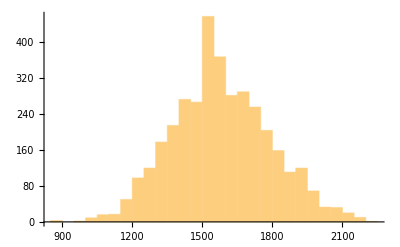

```mathematica
Histogram[allElos]
```

#### Board Data

First we get the “last balanced boards” which is the last two turns of the game where the material is balanced (within 3 points)

```mathematica
matBalances = Map[#["MaterialBalance"]&, boards, {2}];
lbIdxs = getLastBalancedIdx /@ matBalances;
lbLengths = MapThread[Length[#1]+ #2+1&, {fensFiltered, lbIdxs}];
lbIdxsPair = {#-1,#}&/@ lbIdxs;
lbBoardsPair = MapThread[#1[[#2]] &,{boards, lbIdxsPair}] ;
lbBoards = lbBoardsPair[[All, 2]];
```

We sort the boardPairs so that the winner is always the first board, so we can identify the winner easily

```mathematica
lbBoardsPairSorted = MapThread[sortBoardPair[#1, #2]&, {lbBoardsPair, winners}];
```

Next we find the attacked squares of those two boards

```mathematica
attackedSquaresList = Map[#["AttackedSquares"]&, lbBoardsPairSorted, {2}];
attackArrays = Map[getAttackArray, attackedSquaresList, {2}];
winnerAttackArrays = attackArrays[[All, 1]];
loserAttackArrays = attackArrays[[All, 2]];
```

Here I’m going to get the positions of the last boards

```mathematica
positions =getPositions[#["FENString"]]&/@ lbBoards;
whiteIdxs = getWhiteIdxs/@positions;
blackIdxs = getBlackIdxs/@positions;
```

Heat map of the positions

```mathematica
whiteBinArrays = ReplacePart[ConstantArray[0, {8, 8}], #->1]&/@whiteIdxs;
whiteBinArraysSum = Total[whiteBinArrays];
blackBinArrays = ReplacePart[ConstantArray[0, {8, 8}], #->1]&/@blackIdxs;
blackBinArraysSum = Total[blackBinArrays];
winnerBinArrays = MapThread[If[#1 == "White", ReplacePart[ConstantArray[0, {8, 8}], #2->1], ReplacePart[ConstantArray[0, {8, 8}], #3->1]]&, {winners, whiteIdxs, blackIdxs}];
winnerBinArraysSum = Total[winnerBinArrays];
loserBinArrays = MapThread[If[#1 == "White", ReplacePart[ConstantArray[0, {8, 8}], #2->1], ReplacePart[ConstantArray[0, {8, 8}], #3->1]]&, {winners, blackIdxs, whiteIdxs}];
loserBinArraysSum = Total[loserBinArrays];
```

Here we’re looking at the heat map of the positions for the winners and losers

```mathematica
{Grid[winnerBinArraysSum], Grid[loserBinArraysSum]}
```

{740 | 320 | 504 | 512 | 540 | 655 | 830 | 558
941 | 894 | 628 | 395 | 401 | 1077 | 1142 | 991
417 | 390 | 591 | 493 | 566 | 516 | 538 | 493
235 | 360 | 463 | 641 | 715 | 323 | 339 | 264
284 | 312 | 504 | 658 | 646 | 400 | 289 | 235
411 | 418 | 684 | 511 | 475 | 662 | 471 | 517
1080 | 1086 | 828 | 424 | 364 | 1172 | 1364 | 1199
977 | 445 | 603 | 583 | 718 | 651 | 996 | 650,969 | 403 | 625 | 623 | 692 | 778 | 894 | 778
1044 | 981 | 774 | 564 | 517 | 1041 | 1126 | 1087
499 | 428 | 629 | 538 | 580 | 614 | 517 | 530
280 | 383 | 442 | 632 | 674 | 361 | 345 | 290
282 | 357 | 472 | 600 | 624 | 368 | 362 | 273
400 | 390 | 604 | 439 | 418 | 570 | 422 | 517
954 | 887 | 616 | 415 | 330 | 891 | 1027 | 952
811 | 363 | 496 | 487 | 549 | 570 | 769 | 606}

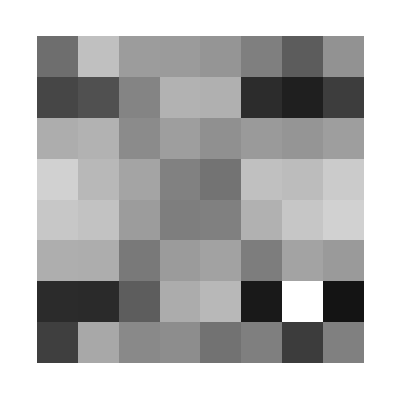
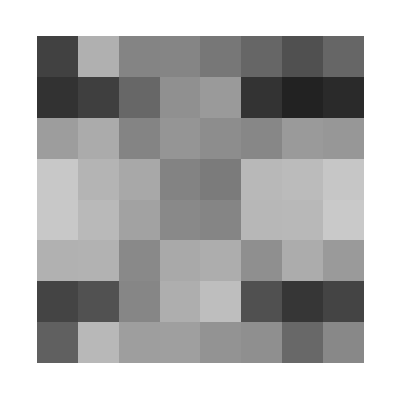

```mathematica
{ArrayPlot[winnerBinArraysSum, PlotRange->{0,1300}], ArrayPlot[loserBinArraysSum, PlotRange->{0,1300}]}
```

Let’s look at where the winners put their queens

Let’s make a function that does this for all pieces

```mathematica
piece = "Q";
res = getWinnerAndLoserPieceHeatArray[piece];
Total[Flatten[#]]&/@res
Grid/@res
ArrayPlot[#, PlotRange->Max[Flatten[res]]]&/@res
ListDensityPlot[Reverse[#], InterpolationOrder->1]&/@res
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[Q].

getWinnerAndLoserPieceHeatArray[Total[Flatten[Q]]]

getWinnerAndLoserPieceHeatArray[Grid[Q]]

ArrayPlot::mat: Argument Q at position 1 is not a list of lists.

getWinnerAndLoserPieceHeatArray[ArrayPlot[Q,PlotRange→getWinnerAndLoserPieceHeatArray[Q]]]

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[Q].

ListDensityPlot::arrayerr: Reverse[Q] must be a valid array.

getWinnerAndLoserPieceHeatArray[ListDensityPlot[Reverse[Q],InterpolationOrder→1]]

Now get the variances

```mathematica
winnerVariances = MapThread[If[#1 == "White", Variance[#2], Variance[#3]]&, {winners, whiteIdxs, blackIdxs}];
loserVariances = MapThread[If[#1 == "White", Variance[#3], Variance[#2]]&, {winners, whiteIdxs, blackIdxs}];
singlePiecePositionsWinners = Rest[Position[winnerVariances,Except[_List], 1]];
singlePiecePositionsLosers = Rest[Position[loserVariances,Except[_List], 1]];
singlePiecePositions = Join[singlePiecePositionsWinners, singlePiecePositionsLosers];
allVariances = Delete[MapThread[{#1, #2}&,{winnerVariances, loserVariances}], singlePiecePositions];
```

Variance::shlen: The argument {{2,5}} should have at least two elements.

Variance::shlen: The argument {{1,8}} should have at least two elements.

Variance::shlen: The argument {{2,6}} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

Variance::shlen: The argument {{5,8}} should have at least two elements.

Variance::shlen: The argument {{8,2}} should have at least two elements.

Variance::shlen: The argument {{1,2}} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

```mathematica
winnerMeanVerticalVariance = N@Mean[allVariances[[All, 1, 2]]]
loserMeanVerticalVariance = N@Mean[allVariances[[All, 2, 2]]]
winnerMeanHorizontalVariance =  N@Mean[allVariances[[All, 1, 1]]]
loserMeanHorizontalVariance =  N@Mean[allVariances[[All, 2, 1]]]
```

5.66101

5.7731

2.25197

2.06911

```mathematica
allVariancesSum =Map[Total, allVariances, {2}];
winnerMeanVariance = N[Mean[allVariancesSum[[All, 1]]]]
loserMeanVariance = N[Mean[allVariancesSum[[All, 2]]]]
```

7.91298

7.84221

#### Get Variances of Random Play

Game length frequencies

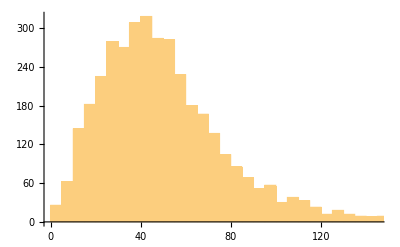

```mathematica
Histogram[lbLengths]
```

```mathematica
randomFENs = RandomChessGame[#]["FENs"][[-1]]&/@ lbLengths
```

```mathematica
randomFENs2 = Delete[randomFENs, singlePiecePositions];
randomWhiteIdxs =getWhiteIdxs[getPositions[#]]&/@ randomFENs2;
randomVars = Variance/@ randomWhiteIdxs;
N@Mean[randomVars[[All, 1]]]
N@Mean[randomVars[[All, 2]]]
```

#### Engine Evaluate

Let’s see if the engine evaluation is a good predictor of outcomes

### Visualization

Total attack squares for winners and losers

```mathematica
Total[winnerAttackArrays, 3]
Total[loserAttackArrays, 3]
```

116651

108196

```mathematica
TableForm[{{Style["Winners", Large], Style["Losers", Large]},
{Grid[Reverse[Total[winnerAttackArrays]]], Grid[Reverse[Total[loserAttackArrays]]]}}]
```

Winners | Losers
1073 | 1531 | 1554 | 1650 | 1618 | 1746 | 1634 | 1321
1306 | 1295 | 1415 | 1713 | 1685 | 1953 | 1678 | 1719
1758 | 1795 | 1972 | 2033 | 2155 | 2192 | 2070 | 1876
1310 | 1959 | 2011 | 2379 | 2287 | 2224 | 2054 | 1564
1407 | 1876 | 2061 | 2316 | 2282 | 2209 | 2043 | 1609
1861 | 2000 | 2084 | 2119 | 2259 | 2303 | 2205 | 2000
1500 | 1349 | 1558 | 1904 | 1853 | 2119 | 1839 | 1865
1119 | 1735 | 1768 | 1877 | 1781 | 1968 | 1801 | 1451 | 1074 | 1663 | 1719 | 1761 | 1730 | 1840 | 1689 | 1205
1390 | 1286 | 1447 | 1797 | 1734 | 1905 | 1622 | 1647
1722 | 1875 | 1930 | 1940 | 2115 | 2119 | 2021 | 1844
1351 | 1881 | 2022 | 2209 | 2106 | 2199 | 1969 | 1438
1348 | 1857 | 1945 | 2149 | 2120 | 2075 | 2022 | 1463
1624 | 1704 | 1792 | 1780 | 1845 | 1933 | 1841 | 1715
1239 | 1129 | 1313 | 1624 | 1536 | 1756 | 1521 | 1505
962 | 1451 | 1482 | 1545 | 1458 | 1580 | 1487 | 1145

Density of attack squares for winners

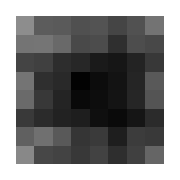
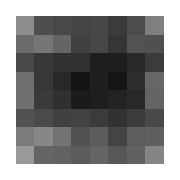
Winners | Losers
-Graphics- | -Graphics-

```mathematica
TableForm[{{Style["Winners", Large], Style["Losers", Large]},
{ArrayPlot[Reverse[Total[winnerAttackArrays]], PlotRange->{0,2400}, ImageSize->Small], ArrayPlot[Reverse[Total[loserAttackArrays]], PlotRange->{0, 2400}, ImageSize->Small]}}]
```

```mathematica
TableForm[{{Style["Winners", Large], Style["Losers", Large]},
{ListDensityPlot[Total[winnerAttackArrays], Mesh->None, InterpolationOrder->1],ListDensityPlot[Total[loserAttackArrays], Mesh->None, InterpolationOrder->1]} }]
```

Winners | Losers
-Graphics- | -Graphics-

```mathematica
attackPlots = Map[ArrayPlot[#, ImageSize->Tiny]&, attackArrays, {2}];
```

Part::take: Cannot take positions 1 through 5 in lbBoardsSorted.

Part::pkspec1: The expression lbBoardsSorted cannot be used as a part specification.

{Winners,Losers}⟦lbBoardsSorted,1;;5⟧

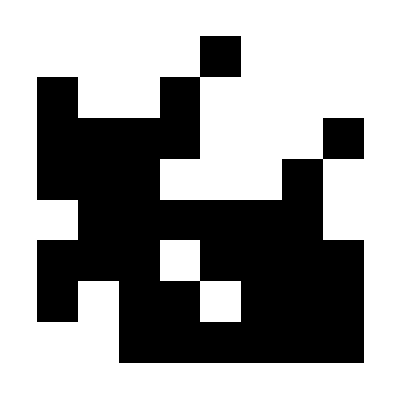
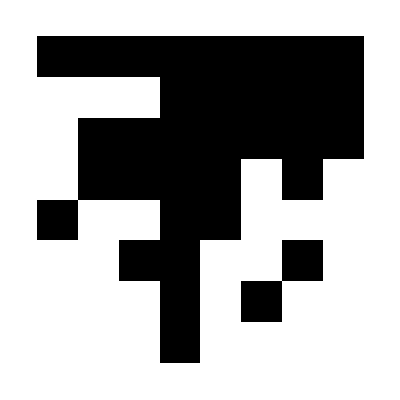
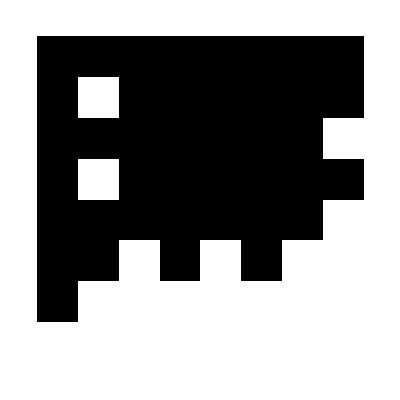
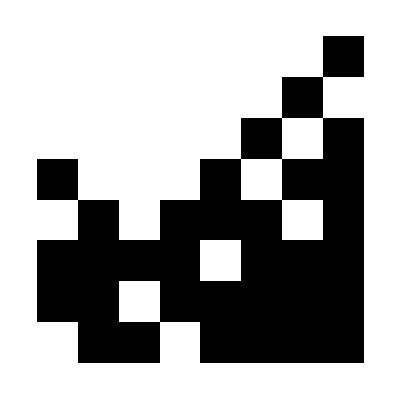
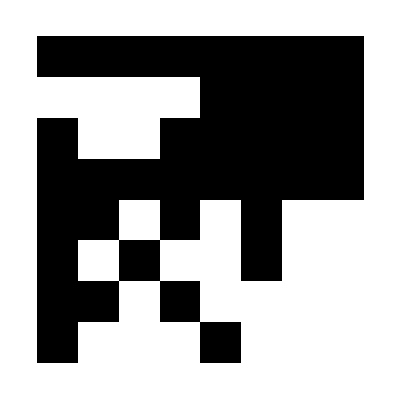
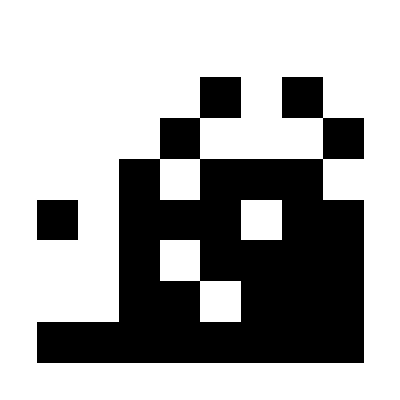
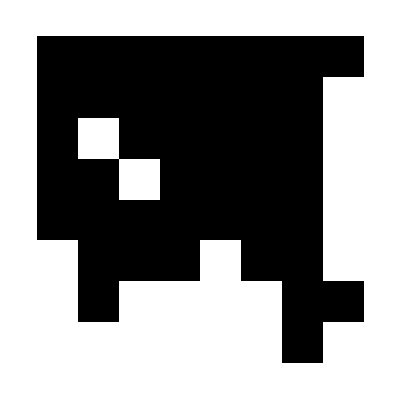
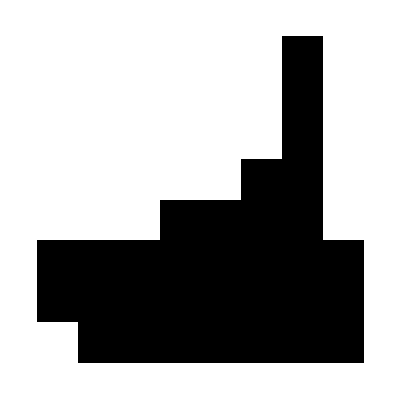
Winners | Losers
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
TableForm[Prepend[attackPlots[[;;5]], {"Winners", "Losers"}]]
```

### Experimentation

```mathematica
lbLengths = MapThread[Length[#1]+ #2+1&, {fensFiltered, lbIdxs}];
```

```mathematica
randomFENs = RandomChessGame[#]["FENs"][[-1]]&/@ lbLengths
```

```mathematica
randomFENs2 = Delete[randomFENs, singlePiecePositions];
```

```mathematica
randomWhiteIdxs =getWhiteIdxs[getPositions[#]]&/@ randomFENs2;
```

```mathematica
randomVars = Variance/@ randomWhiteIdxs;
```

```mathematica
N@Mean[randomVars[[All, 1]]]
```

2.40646

```mathematica
N@Mean[randomVars[[All, 2]]]
```

5.75532

```mathematica
positions[[1]]
```

{{k,0,0,r,0,b,n,r},{n,Q,p,q,p,0,p,p},{0,0,0,0,0,p,0,0},{0,0,0,p,0,0,0,0},{0,0,0,P,0,B,0,0},{P,0,N,0,P,0,0,0},{0,0,P,0,0,P,P,P},{0,R,0,0,K,0,N,R}}

```mathematica
whiteQueenIdxs =Position[#, "Q"]&/@ positions
```

```mathematica
whiteQueenBinArrays = ReplacePart[ConstantArray[0, {8, 8}], #->1]&/@whiteQueenIdxs;
whiteQueenBinArraysSum = Total[whiteQueenBinArrays];
whiteWinnerPositions = Flatten[Position[winners, "White"]];
blackWinnerPositions = Flatten[Position[winners, "Black"]];
onlyWinnerWhiteQueens = whiteQueenBinArrays[[whiteWinnerPositions]];
onlyLoserWhiteQueens = whiteQueenBinArrays[[blackWinnerPositions]];
onlyWinnerWhiteQueensSum  = Total[onlyWinnerWhiteQueens];
onlyLoserWhiteQueensSum  = Total[onlyLoserWhiteQueens];
```

{9 | 4 | 3 | 10 | 7 | 3 | 5 | 19
10 | 26 | 14 | 10 | 10 | 52 | 23 | 30
12 | 11 | 12 | 13 | 23 | 19 | 12 | 28
6 | 9 | 6 | 17 | 27 | 10 | 7 | 25
20 | 5 | 22 | 19 | 15 | 15 | 23 | 17
6 | 28 | 21 | 31 | 24 | 55 | 26 | 8
2 | 9 | 44 | 46 | 52 | 10 | 7 | 2
3 | 6 | 4 | 234 | 7 | 4 | 2 | 1,11 | 6 | 5 | 5 | 8 | 3 | 3 | 9
8 | 10 | 7 | 8 | 4 | 10 | 4 | 5
6 | 5 | 11 | 10 | 11 | 9 | 4 | 12
8 | 4 | 6 | 20 | 12 | 16 | 15 | 21
15 | 10 | 11 | 17 | 17 | 12 | 28 | 18
0 | 21 | 23 | 33 | 36 | 63 | 20 | 15
6 | 10 | 31 | 55 | 52 | 20 | 4 | 2
5 | 9 | 8 | 171 | 14 | 11 | 4 | 3}

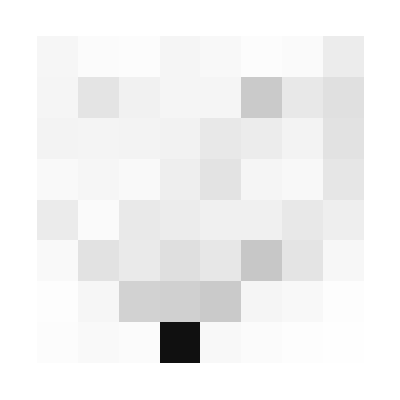
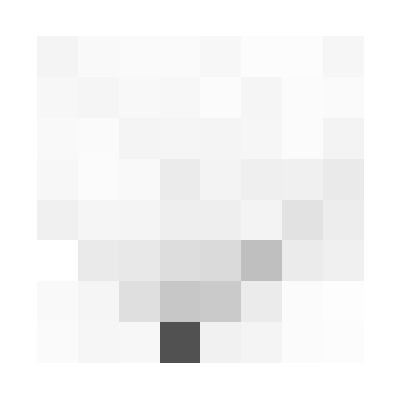

```mathematica
{Grid[onlyWinnerWhiteQueensSum], Grid[onlyLoserWhiteQueensSum]}
ArrayPlot[#, PlotRange->250]&/@{onlyWinnerQueensSum, onlyLoserWhiteQueensSum}
```